# Лабораторная работа 2 Крощук Виктор, ПО5 Задание 1 №1

```mathematica
t1 =  (4(x^3+ 9)(x^2-y^2))/((9 x^2-16)(x-y))+2(x+y)^2+x^3+y^3

(*Функция раскрывает скобки в алгебраическом вывражении. Позволяет представить выражение в виде суммы рациональных выражений. однако не раскрыввает скобки в знаменателе*)

Expand[t1]
```

x^3+y^3+2 (x+y)^2+(4 (9+x^3) (x^2-y^2))/((-16+9 x^2) (x-y))

2 x^2+x^3+(36 x^2)/((-16+9 x^2) (x-y))+(4 x^5)/((-16+9 x^2) (x-y))+4 x y+2 y^2-(36 y^2)/((-16+9 x^2) (x-y))-(4 x^3 y^2)/((-16+9 x^2) (x-y))+y^3

```mathematica
x^3+y^3+2 (x+y)^2+(4 (9+x^3) (x^2-y^2))/((-16+9 x^2) (x-y))
```

x^3+y^3+2 (x+y)^2+(4 (9+x^3) (x^2-y^2))/((-16+9 x^2) (x-y))

```mathematica
(*Расскрыввет скобки как в числителе, так и в знаменателе*)

ExpandAll[t1]
```

2 x^2+x^3+4 x y+2 y^2+y^3+(36 x^2)/(-16 x+9 x^3+16 y-9 x^2 y)+(4 x^5)/(-16 x+9 x^3+16 y-9 x^2 y)-(36 y^2)/(-16 x+9 x^3+16 y-9 x^2 y)-(4 x^3 y^2)/(-16 x+9 x^3+16 y-9 x^2 y)

```mathematica
(*для того, чтобы преставить многочлен в виде произвеения многочленов (нашли общий множитель)*)
Factor[t1]
```

1/((-4+3 x) (4+3 x))(x+y) (36-32 x-16 x^2+22 x^3+9 x^4-32 y+16 x y+18 x^2 y-9 x^3 y-16 y^2+9 x^2 y^2)

```mathematica
(*Находим общий знаминатель и складываем многочлены*)
Together[t1]
```

1/(-16+9 x^2)(36 x-32 x^2-16 x^3+22 x^4+9 x^5+36 y-64 x y+40 x^3 y-32 y^2+18 x^2 y^2-16 y^3+9 x^2 y^3)

```mathematica
(*Записываем функциональное выражение в ввиде суммы членов с минимальными знаминателями. Производит разложение дробей.*)
Apart[t1]
```

(x (36-32 x-16 x^2+22 x^3+9 x^4))/((-4+3 x) (4+3 x))+(4 (9-16 x+10 x^3) y)/((-4+3 x) (4+3 x))+2 y^2+y^3

```mathematica
(* сокращаем общие множители в числе и заминателе рационального выражения*)
Cancel[t1]
```

x^3+y^3+(4 (9+x^3) (x+y))/(-16+9 x^2)+2 (x+y)^2

```mathematica
(*Последователбьность алгебраических преобразований и упрощает выражение*)
Simplify[t1]
```

x^3+y^3+(4 (9+x^3) (x+y))/(-16+9 x^2)+2 (x+y)^2

№2

```mathematica
(*Извлеките числитель рационального выражения*)
f2=Numerator[Together[t1]];f2
```

36 x-32 x^2-16 x^3+22 x^4+9 x^5+36 y-64 x y+40 x^3 y-32 y^2+18 x^2 y^2-16 y^3+9 x^2 y^3

```mathematica
(*обирает вместе термины,включающие одинаковые степени объектов,соответствующих x.*)
Collect[f2,x]
```

22 x^4+9 x^5+x (36-64 y)+36 y-32 y^2-16 y^3+x^3 (-16+40 y)+x^2 (-32+18 y^2+9 y^3)

```mathematica
Collect[f2,y]
```

36 x-32 x^2-16 x^3+22 x^4+9 x^5+(36-64 x+40 x^3) y+(-32+18 x^2) y^2+(-16+9 x^2) y^3

# Задание 2

№1

```mathematica
(*дает полная производную*)
D[x^n  Cos[x],x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

№2

```mathematica
D[(a x^3+2 x^2),x]
```

4 x+3 a x^2

```mathematica
(*дает кратную производную*)
D[(4 x^2-5 x+8-3/x),{x,3}]
```

18/x^4

```mathematica
(*дает кратную частную производную*)
D[(x^3 y^2+3 x^2),{x,3},{y,2}]
```

12

№3

```mathematica
(*дает неопределенный интеграл*)
Integrate[ 1/(x^2-1),x]
```

1/2 Log[1-x]-1/2 Log[1+x]

№4

```mathematica
Integrate[x^3/(x^2+1),x]
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Integrate[1/(x^3+1),x]
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
(*складывает члены в сумму по общему знаменателю и отменяет множители в результате*)

Together[D[x^2/2-1/2 Log[1+x^2],x]]
```

x^3/(1+x^2)

```mathematica
(*Расскрыввет скобки как в числителе, так и в знаменателе*)
ExpandAll[Together[D[ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2],x]]]
```

1/(1+x^3)

№5

```mathematica
(*определенный интеграл от 1 до 4 по dx*)
∫_1^4 (5x-2√x+32/x^3)ⅆx
```

259/6

№6

```mathematica
(*от 0 до 1 получаем точный результат. Целое число*)
∫_0^1 (1+x^4)^(1/3)ⅆx
```

1/7 (3 2^(1/3)+4 Hypergeometric2F1[1/4,2/3,5/4,-1])

```mathematica
(*приближенный. 1. относиться к дйствительным*)
∫_0^1. (1+x^4)^(1/3)ⅆx
```

1.05753

# Задание 3

№1

```mathematica
(*находим множество конрней над полем комплексных чисел*)
Solve[a x^4+x^2+3==0,x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

№2

```mathematica
(*решаем систему. Соединяем два уравлнения гиперсантом {}* )
Solve[x^2+y==1 && y^2-x^2==2,{x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

№3

```mathematica
(*получаем приближенное численное решение*)
NSolve[x^2-y^2==1 && y^3+x==5,{x,y}]
```

{{x→-2.17236,y→1.9285},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.78303,y→1.47621},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ}}

№4

```mathematica
(*решаем диференциальное уравнение 1. Получили общее решение*)
DSolve[{y'[x]-y[x]*Tan[x]==x,y[0]==0},y[x], x]
```

{{y[x]→1-Sec[x]+x Tan[x]}}

```mathematica
DSolve[{y'[x]+y[x]*Tan[x]==1/Cos[x],y[0]==0},y[x],x]
```

{{y[x]→Sin[x]}}

№5

```mathematica
(*построили график. Частного решения. Далее находим общее решение, заьем строим график частного решения. Далее решаем диференциальное уравнение, причем
мы задаем начальное условие. Ч р., числ. р, прибл.*)

DSolve[{y'[x]-y[x]*Tan [x]==x,y[0]==0},y[x-],x]
```

{{y[x]→1-Sec[x]+x Tan[x]}}

```mathematica
t3= DSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], x] //FullSimplify
```

{{y[x]→1/2 ⅇ^(x/2) π (-((AiryAi[1/4]+2 AiryAiPrime[1/4]) AiryBi[1/4-x])+AiryAi[1/4-x] (AiryBi[1/4]+2 AiryBiPrime[1/4]))}}

```mathematica
t4 = NDSolve[{y''[x]-y'[x]+x y[x]==0, y[0]==1, y'[0]==1}, y[x], {x, -7,7}]
```

{{y[x]→InterpolatingFunction[…][x]}}

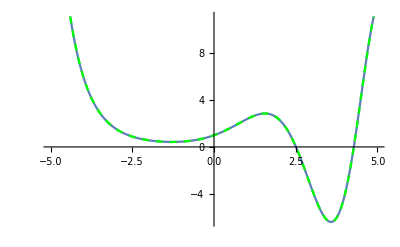

```mathematica
finalTask = Show[Plot[t3[[1,1,2]],{x,-5,5}], Plot[t4[[1, 1, 2]], {x, -5, 5},PlotStyle->{Dashed, Green}]]
```